```mathematica
img = ExampleData[{"TestImage", "Mandrill"}]
```

-Graphics-

```mathematica
grayImg = ColorConvert[img, "Grayscale"]
```

-Graphics-

```mathematica
grayImgData = ImageData[grayImg, "Byte"];
```

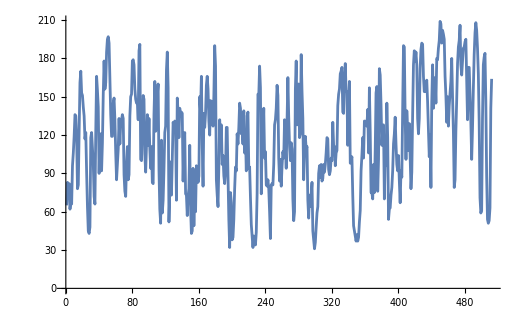

```mathematica
ListPlot[{grayImgData[[100]]}, Joined->True]
```

```mathematica
Dimensions[grayImgData[[100]]]
```

{512}

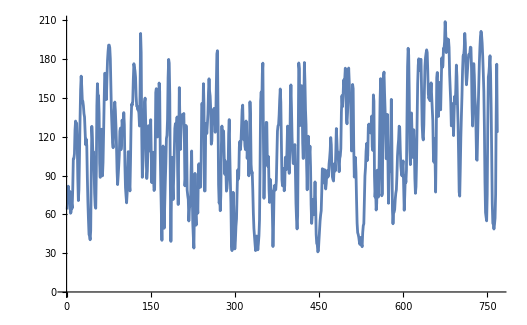

```mathematica
row = N[grayImgData[[100]]];
n   = Length[row];
{min, max} = MinMax[row];
fft  = Fourier[row];
zero = ConstantArray[0., 256];

mid  = Floor[Length[fft]/2];
padFFT = Join[Take[fft, mid], zero, Drop[fft, mid]];
inv    = InverseFourier[padFFT];
minmaxInv = MinMax[Re[inv]];
output = Rescale[Re[inv], minmaxInv, {min, max}];
ListPlot[{output}, Joined->True]
```

```mathematica
UpscaleImg[grayImgData_, pS_] := Module[{row, n, min, max,fft, padFFT, inv, minmaxInv, output, nRow, res={}, i, mid, zero},
	nRow = Length[grayImgData];
	For[i = 1, i <= nRow, i++,
		row = N[grayImgData[[i]]];
		n   = Length[row];
		{min, max} = MinMax[row];
		fft = Fourier[row];
		zero = ConstantArray[0., pS];
		mid  = Floor[Length[fft]/2];
		padFFT = Join[Take[fft, mid], zero, Drop[fft, mid]];
		inv = InverseFourier[padFFT];
		
		minmaxInv = MinMax[Re[inv]];
		output = Rescale[Re[inv], minmaxInv, {min, max}];
		AppendTo[res, output];
	
	];
	Return[res];
	
]
```

```mathematica
datX = UpscaleImg[grayImgData, 256];
datY = Transpose[UpscaleImg[Transpose[datX], 256]];
Image[datY, "Byte"]
```

-Graphics-

```mathematica
ExampleData["Dataset"]
```

{{Dataset,Planets},{Dataset,StatePopulations},{Dataset,Titanic}}